```mathematica
Solve[D[ (ℏ^2)/(8x)+(m ω^2)/2 x]==0,x]
```

{{x→-(ⅈ ℏ)/(2 √m ω)},{x→(ⅈ ℏ)/(2 √m ω)}}

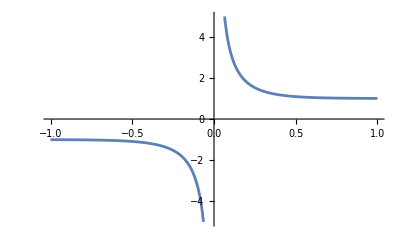

```mathematica
Plot[Coth[x π],{x,-1,1}]
```

```mathematica
Integrate[κ E^(2 κ x),{x,0,∞}]
```

ConditionalExpression[-1/2, Re[κ]<0]

```mathematica
Sqrt[1+x]+Sqrt[1-x]
```

√(1-x)+√(1+x)

```mathematica
Simplify[%]
```

√(1-x)+√(1+x)

```mathematica
V = Integrate[Sqrt[1+4/π^2],{s,0,2π}]
```

2 √(1+4/π^2) π

```mathematica
W = Integrate[Sqrt[4+π^2],{s,0,2π}]
```

2 π √(4+π^2)

```mathematica
V === W
```

False

```mathematica
M = {{0,1},{1,0}}
```

{{0,1},{1,0}}

```mathematica
MatrixForm[M]
```

(0 | 1
1 | 0)

```mathematica
f = ⅇ^(-(x-x0)^2/(4σ^2))
```

ⅇ^(-(x-x0)^2/(4 σ^2))

```mathematica
D[f,x]
```

-(ⅇ^(-(x-x0)^2/(4 σ^2)) (x-x0))/(2 σ^2)

```mathematica
D[%,x]
```

(ⅇ^(-(x-x0)^2/(4 σ^2)) (x-x0)^2)/(4 σ^4)-(ⅇ^(-(x-x0)^2/(4 σ^2)))/(2 σ^2)

```mathematica
Cos[θ]-Cos[2θ]
```

Cos[θ]-Cos[2 θ]

```mathematica
Simplify[%]
```

Cos[θ]-Cos[2 θ]

```mathematica
Abs[x]
```

Abs[x]

```mathematica
D[Abs[x],x]
```

Abs'[x]

```mathematica
M = {{0,1},{1,0}}
```

{{0,1},{1,0}}

```mathematica
MatrixForm[M]
```

(0 | 1
1 | 0)

```mathematica
f = ⅇ^(-(x-x0)^2/(4σ^2))
```

ⅇ^(-(x-x0)^2/(4 σ^2))

```mathematica
D[f,x]
```

-(ⅇ^(-(x-x0)^2/(4 σ^2)) (x-x0))/(2 σ^2)

```mathematica
D[%,x]
```

(ⅇ^(-(x-x0)^2/(4 σ^2)) (x-x0)^2)/(4 σ^4)-(ⅇ^(-(x-x0)^2/(4 σ^2)))/(2 σ^2)

```mathematica
Sin[x]/Cos[x]
```

Tan[x]

```mathematica
func = 1/Sin[θ]
```

Csc[θ]

```mathematica
D[func,θ]
```

-Cot[θ] Csc[θ]

```mathematica
Csc[θ]===1/Sin[θ]
```

True

```mathematica
ψ =A ⅇ^(-k x)
```

A ⅇ^(-k x)

```mathematica
Simplify[Integrate[Abs[ψ]^2,{x,0,∞}]== 1, Assumptions->k ∈ Reals]
```

ConditionalExpression[2 k==Abs[A]^2, k>0]

```mathematica
σx =MatrixForm[{{0,1},{1,0}}]
```

(0 | 1
1 | 0)

```mathematica
Simplify[MatrixForm[σx * σx]]
```

(0 | 1
1 | 0)^2

```mathematica
Eigenvectors[{{1,0},{0,-1}}]
```

{{0,1},{1,0}}

```mathematica
Arg
```

```mathematica
Integrate[x Sin[π x/L]Sin[2π x/L],{x,0,L}]
```

-(8 L^2)/(9 π^2)

```mathematica
Simplify[Sin[k1 x]Cos[k1 x]]
```

Cos[k1 x] Sin[k1 x]

```mathematica
test = Sin[n π x/L]
```

Sin[(n π x)/L]

```mathematica
D[test,{x,2}]
```

-(n^2 π^2 Sin[(n π x)/L])/L^2

```mathematica
ψ = a1*Sin[n1 π x/L]+ a2*Sin[n2 π x/L]
```

a1 Sin[(n1 π x)/L]+a2 Sin[(n2 π x)/L]

```mathematica
Simplify[BraKet[{ψ},{ψ}],Assumptions->{a1 ∈ Complexes,a2 ∈Complexes}]
```

a1 Sin[(n1 π x)/L]+a2 Sin[(n2 π x)/L]a1 Sin[(n1 π x)/L]+a2 Sin[(n2 π x)/L]

```mathematica
Integrate[ψ*ψ,x,Assumptions->{a1 ∈ Complexes,a2 ∈Complexes} ]
```

Integrate[Conjugate[a1 Sin[(n1 π x)/L]+a2 Sin[(n2 π x)/L]] (a1 Sin[(n1 π x)/L]+a2 Sin[(n2 π x)/L]),x,Assumptions→{a1∈ℂ,a2∈ℂ}]